```mathematica
ParallelEvaluate[Off[General::munfl,FindFit::cvmit]];
Off[General::munfl,General::stop,LinearSolve::luc,FindFit::cvmit]
SetDirectory[NotebookDirectory[]]
```

/home/johannesk/kette_repo/limit_cycles/src_mathematica/good_fits

```mathematica
(* Nuclear E2=2.22 E3=8.48 ℏc=198*)
LECsNUCL=Import["../LECs_nucl_Joki.dat","Table"][[2;;]];

activeLEC=LECsNUCL[[All,{1,2,3}]];
```

```mathematica
hbar=197.327053;
Mm=938.92;
m1=3 Mm;m2=3 Mm;
μ=m1 m2/(m1+m2);
mh2=(2 μ)/(hbar)^2;
Print["ℏ^2/(2  μ) = ",1/mh2]

dimerCores={{2.00,{{3.49894,20.5763},{1.31002,2.03082},{0.230922,56.5742},{0.136023,20.549},{0.146917,20.5961}}}};
λRange=Range[1,Length[activeLEC]];
```

ℏ^2/(2  μ) = 13.8237

```mathematica
RiccatiBesselJ[z_,l_]:=z SphericalBesselJ[l,z];
RiccatiBesselN[z_,l_]:=(-1)^l z SphericalBesselY[l,z];
```

```mathematica
(*Boundery conditions for the wavefunction*)
alpha[ra_,ka_,la_,ha_]:=RiccatiBesselN[ka (ra+ha),la]/RiccatiBesselN[ka ra,la]

beta[rb_,kb_,lb_,hb_]:=RiccatiBesselJ[kb (rb+hb),lb]-RiccatiBesselJ[kb rb,lb] (RiccatiBesselN[kb (rb+hb),lb]/RiccatiBesselN[kb rb,lb])
```

```mathematica
NormTT[core_?ArrayQ]:=Total[Flatten[Table[core[[i]][[1]] core[[j]][[1]]core[[k]][[1]]core[[l]][[1]] (Pi^4/(3^2 ((core[[i]][[2]]+core[[j]][[2]])^2 (core[[k]][[2]]+core[[l]][[2]])^2)))^(3/2),{i,Length[core]},{j,Length[core]},{k,Length[core]},{l,Length[core]}]]];

VlocTF[r_,lam_,Cc_,Dd_,Aa_,Bb_,Gg_,Hh_]:=Block[{eta1,eta2,eta3,w1,w2,w3},
eta2= 3^(7/2)Cc /(((Aa+Bb)(Gg+Hh)(2 lam Bb+Gg(2 lam+3Bb)+2 lam Hh+3Bb Hh+Aa(2 lam+3Gg+3Hh)))^(3/2));
w2= 3(Aa+Bb)(Gg+Hh)lam/(2lam Bb+Gg(2 lam+3Bb)+2 lam Hh+3Bb Hh+Aa(2lam+3Gg+3Hh));
eta3 =3^(7/2)Dd /(((Aa+Bb)(lam+Gg+Hh)(lam Bb+Gg(4lam+3Bb)+4 lam Hh+3Bb Hh+Aa(lam+3Gg+3Hh)))^(3/2));
w3 = 6(Aa+Bb)(Gg+Hh)lam/(lam Bb+Gg(4 lam+3Bb)+4 lam Hh+3Bb Hh+Aa(lam+3Gg+3Hh));
eta1 =3^(7/2)Dd /(((Gg+Hh)(4 lam^2 Bb+2lam Bb^2+Gg(lam^2+8 lam Bb+3Bb^2)+lam^2 Hh+8 lam Bb Hh+3Bb^2 Hh+Aa^2(2lam+3Gg+3Hh)+Aa(Gg(8 lam+6Bb)+4lam(lam+2Hh)+Bb(4lam+6Hh))))^(3/2));
w1=(3(Aa+Bb)lam(Aa+Bb+2lam)(Gg+Hh))/((4 lam^2 Bb+2lam Bb^2+Gg(lam^2+8 lam Bb+3Bb^2)+lam^2 Hh+8 lam Bb Hh+3Bb^2 Hh+Aa^2(2lam+3Gg+3Hh)+Aa(Gg(8 lam+6Bb)+4lam(lam+2Hh)+Bb(4lam+6Hh))));
eta2 Exp[-w2 r^2]+eta3 Exp[-w3 r^2]+eta1 Exp[-w1 r^2]
];

WnolocTF[r_,rp_,Ee_,lam_,Cc_,Dd_,Aa_,Bb_,Gg_,Hh_,Ll_,TwoMyOverHBsq_]:=Block[{zeta1,zeta2,zeta3,a1,b1,c1,a2,b2,c2,a3,b3,c3},
zeta1=0;
a1=4Bb Hh + Gg Bb+Gg Hh+Aa Bb +Aa Hh;
b1=2Gg Bb -Gg Hh -2 Aa Bb +2 Aa Hh;
c1=Gg Bb +Hh Gg+4Aa Gg +Aa Bb +Aa Hh;

zeta2=0;
zeta3=0;

a2=4Hh(2lam+Bb)+Gg(2lam +Bb+Hh)+Aa(2lam+Bb+Hh);
b2=Gg(4lam+2Bb-2 Hh)+Aa(-4lam-2Bb+2Gg);
c2=Gg(2lam+Bb+Hh)+Aa(2lam+4Gg+Bb+Hh);

a3= 4Bb(2lam+Hh)+Gg(Aa+2lam+Hh)+Aa(2lam+Bb+Hh);
b3=Gg(2Bb-4lam-2Hh)+Aa(4lam+2Hh-2Bb);
c3=Gg(Bb+2lam+Hh)+Aa(4Gg+2lam+Bb+Hh);

-(4 Pi r rp) (
zeta1 Exp[-a1 r^2-c1 rp^2] ((-(4 a1^2 r^2+b1^2 rp^2-2 a1)+(Ll+1) Ll/r^2-TwoMyOverHBsq Ee) I^Ll  SphericalBesselJ[Ll,I b1 r rp]
-4 a1 b1 r rp Sum[(1-Ll^2+l^2) I^(l+1)/Sqrt[3] (2/Sqrt[5])^((Ll+l)/2) SphericalBesselJ[1+l,I b1 r rp],{l,-Ll,Ll}])
+I^Ll zeta2 SphericalBesselJ[Ll,I b2 r rp] Exp[-a2 r^2-c2 rp^2]
+I^Ll zeta3 SphericalBesselJ[Ll,I b3 r rp] Exp[-a3 r^2-c3 rp^2]
)
];
```

```mathematica
SolveSecular[Rdis_?NumberQ,Npoints_?NumberQ,momentum_?NumberQ,Lin_?NumberQ,lam_?NumberQ,c0_?NumberQ,d0_?NumberQ,a00_?ArrayQ,TwoMyOverHBsq_?NumberQ]:=Block[{hDif,Dmat,Kmat,Wmat,bcol,Amat,ucol,wf,tanDelta,usol,energyMeV,nff,cij},

hDif=Rdis/Npoints;
energyMeV=(momentum^2)/TwoMyOverHBsq;
Kmat=SparseArray[{Band[{1,1}]->-2,Band[{2,1}]->1,Band[{1,2}]->1},{Npoints,Npoints}];

normsqu=1./NormTT[a00];

Wmat=ConstantArray[0,{Npoints,Npoints}];

prefac=(*(4 π)^1.5*)1;

Wmatt=ParallelTable[
cij=a00[[ii]][[1]] a00[[jj]][[1]] a00[[kk]][[1]]  a00[[ll]][[1]]  normsqu;
DiagonalMatrix[Table[-cij hDif^2 TwoMyOverHBsq VlocTF[i hDif,lam,c0,d0,a00[[ii]][[2]],a00[[jj]][[2]],a00[[kk]][[2]],a00[[ll]][[2]]],{i,1,Npoints}]]
,{ii,1,Length[a00]},{jj,1,Length[a00]},{kk,1,Length[a00]},{ll,1,Length[a00]}];

Wmat=Total[Wmatt,4];
Dmat=DiagonalMatrix[Table[hDif^2 (momentum^2-(Lin (Lin+1))/(i hDif)^2),{i,1,Npoints}]];
(*Print[(Chop[Wmat])[[1;;4,1;;4]]//MatrixForm];*)
Amat=Kmat+Dmat+Wmat;

bcol=ConstantArray[0,Npoints];
ucol=Array[Subscript["u", ##]&,{Npoints}];

bcol⟦-1⟧=- beta[Rdis,momentum,Lin,hDif];
Amat⟦-1⟧⟦-1⟧=Amat⟦-1⟧⟦-1⟧+alpha[Rdis,momentum,Lin,hDif];

usol=LinearSolve[Amat,bcol];

tanDelta= (RiccatiBesselJ[momentum  Rdis,Lin]/RiccatiBesselN[momentum Rdis,Lin])-(usol⟦-1⟧/RiccatiBesselN[momentum Rdis,Lin]);
(*Print["N_terms = ",Length[a00]^4," calculated for E_rel = ",energyMeV," MeV"];*)
tanDelta
];
```

```mathematica
GetERE[l_,rMax_,nPoints_,core_]:=Module[{locall=l},

dataS={};
tanDsL={};
tanDs={};

eRange=Range[0.01,0.1,0.03];

LECc = Flatten[Select[activeLEC,#[[1]]==locall&]][[2]];
LECd = Flatten[Select[activeLEC,#[[1]]==locall&]][[3]];

SetSharedVariable[tanDs];

Do[
momFM=Sqrt[mh2 energ];
TanDelSwave=SolveSecular[rMax,nPoints,momFM,0,locall,LECc,LECd,core,mh2];
AppendTo[tanDs,{energ,TanDelSwave}];
,{energ,eRange}];

tanDs=Reverse[Sort[tanDs,#1[[1]]>#2[[1]]&]]; (*Sort all the momentum since it is parallel*)

(*Extract the ERE Parameters*)
Lrel = 0;
dataS=Transpose[{Sqrt[mh2 eRange],Sqrt[mh2 eRange ]/Re[tanDs⟦All,2⟧]}];
EreS=Fit[dataS⟦1;;3⟧,{1,p^2},p];
a0tf=-Coefficient[EreS,p,0]^-1;
r0tf= Coefficient[EreS,p,2]*2.;
{a0tf,r0tf,dataS}
]
```

```mathematica
JacobiWavefunctions={
{2.0,{{-0.01061740,4.13404400,0.27286900},{0.00820667,4.13404400,0.18057100},{-0.00232704,4.13404400,0.06354700},{0.00663043,3.47668300,0.27286900},{0.00824312,3.47668300,0.18057100},{0.00882996,3.47668300,0.06354700},{0.48249900,1.41086700,0.27286900},{-0.05509460,1.41086700,0.18057100},{0.31809900,1.41086700,0.06354700},{-0.50162500,1.26632400,0.27286900},{0.07544860,1.26632400,0.18057100},{-0.33183300,1.26632400,0.06354700},{0.17321700,0.84262700,0.27286900},{0.03289340,0.84262700,0.18057100},{0.16311400,0.84262700,0.06354700},{-2.13230000,0.25662000,0.27286900},{3.18971000,0.25662000,0.18057100},{-0.27975700,0.25662000,0.06354700},{2.45883000,0.24733700,0.27286900},{-3.86811000,0.24733700,0.18057100},{0.44169500,0.24733700,0.06354700},{0.00315959,0.00556100,0.27286900},{-0.00699255,0.00556100,0.18057100},{0.01162550,0.00556100,0.06354700},{0.00052919,9.20551700,1.90963000},{-0.00090575,9.20551700,0.22164800},{-0.00019846,9.20551700,0.06304600},{0.05794020,1.92216500,1.90963000},{-0.09777030,1.92216500,0.22164800},{-0.10221100,1.92216500,0.06304600},{-0.03306620,1.31386900,1.90963000},{0.06791630,1.31386900,0.22164800},{0.20769300,1.31386900,0.06304600},{0.03301990,1.00860000,1.90963000},{-0.15354300,1.00860000,0.22164800},{-0.25679100,1.00860000,0.06304600},{-0.01307010,0.22007800,1.90963000},{0.00014706,0.22007800,0.22164800},{-0.12907900,0.22007800,0.06304600},{0.02167700,0.12481900,1.90963000},{-1.04734000,0.12481900,0.22164800},{-0.32768600,0.12481900,0.06304600},{-0.02038300,0.08951100,1.90963000},{0.77814700,0.08951100,0.22164800},{0.75664800,0.08951100,0.06304600},{0.00690824,0.07059200,1.90963000},{-0.24339700,0.07059200,0.22164800},{-0.59746100,0.07059200,0.06304600}}},
{4.0,{{-0.00458098,10.55522400,4.77353400},{0.01136790,10.55522400,0.50551500},{0.02270740,10.55522400,0.11475700},{-0.04961920,5.06681000,4.77353400},{0.06063370,5.06681000,0.50551500},{0.06508300,5.06681000,0.11475700},{-0.34673700,1.60615500,4.77353400},{0.35959000,1.60615500,0.50551500},{1.24912000,1.60615500,0.11475700},{0.51247900,1.41350500,4.77353400},{-0.79196700,1.41350500,0.50551500},{-2.56730000,1.41350500,0.11475700},{-0.19744800,1.25872800,4.77353400},{0.56620100,1.25872800,0.50551500},{1.53940000,1.25872800,0.11475700},{0.00115267,0.33103800,4.77353400},{-0.01668790,0.33103800,0.50551500},{-0.12163300,0.33103800,0.11475700},{-0.00096886,0.27555800,4.77353400},{-0.02503190,0.27555800,0.50551500},{0.44081300,0.27555800,0.11475700},{0.00036285,0.05549300,4.77353400},{-0.00574768,0.05549300,0.50551500},{0.07541940,0.05549300,0.11475700},{0.00912753,11.52004800,1.15339600},{-0.02106490,11.52004800,0.26045100},{-0.00927716,11.52004800,0.06921300},{-0.02952810,6.93907300,1.15339600},{-0.01076950,6.93907300,0.26045100},{-0.01134370,6.93907300,0.06921300},{-0.02627570,3.73198100,1.15339600},{-0.09169450,3.73198100,0.26045100},{-0.06370020,3.73198100,0.06921300},{0.04294550,1.02516800,1.15339600},{-0.15630900,1.02516800,0.26045100},{-0.09345540,1.02516800,0.06921300},{0.01720450,0.29212900,1.15339600},{-0.10470700,0.29212900,0.26045100},{-0.17589800,0.29212900,0.06921300},{-0.02948640,0.10880500,1.15339600},{0.28674000,0.10880500,0.26045100},{0.25576700,0.10880500,0.06921300},{0.01889250,0.07992100,1.15339600},{-0.14249100,0.07992100,0.26045100},{-0.28664400,0.07992100,0.06921300},{-0.00035011,0.00212900,1.15339600},{0.00208741,0.00212900,0.26045100},{-0.00418899,0.00212900,0.06921300}}},
{6.0,{{0.00062059,22.11367000,7.18348300},{0.01211750,22.11367000,0.64982000},{0.02221600,22.11367000,0.11860500},{-0.04489910,10.20688800,7.18348300},{0.04803360,10.20688800,0.64982000},{0.06331490,10.20688800,0.11860500},{-23.06490000,3.17864800,7.18348300},{55.03550000,3.17864800,0.64982000},{35.77350000,3.17864800,0.11860500},{23.02960000,3.17669500,7.18348300},{-55.05410000,3.17669500,0.64982000},{-35.70400000,3.17669500,0.11860500},{-0.00348992,1.77152600,7.18348300},{0.19498800,1.77152600,0.64982000},{0.09566220,1.77152600,0.11860500},{-0.00099838,0.58969500,7.18348300},{-0.16368300,0.58969500,0.64982000},{0.19464400,0.58969500,0.11860500},{-0.00002652,0.12010900,7.18348300},{-0.00191004,0.12010900,0.64982000},{0.28231900,0.12010900,0.11860500},{0.00021903,0.02707800,7.18348300},{-0.00403877,0.02707800,0.64982000},{0.05870350,0.02707800,0.11860500},{0.15210800,11.01490100,1.76242800},{-0.60825100,11.01490100,0.45681100},{-0.53017300,11.01490100,0.09890900},{-0.19106400,9.93859100,1.76242800},{0.71844400,9.93859100,0.45681100},{0.62131800,9.93859100,0.09890900},{0.01916960,6.75448800,1.76242800},{-0.22536400,6.75448800,0.45681100},{-0.21887800,6.75448800,0.09890900},{0.22475600,1.17395700,1.76242800},{-0.79114000,1.17395700,0.45681100},{-1.10797000,1.17395700,0.09890900},{-0.16637900,1.08075000,1.76242800},{0.75193900,1.08075000,0.45681100},{1.13919000,1.08075000,0.09890900},{0.01603430,0.58720700,1.76242800},{-0.26600000,0.58720700,0.45681100},{-0.32337200,0.58720700,0.09890900},{-0.00232547,0.20157400,1.76242800},{0.01257080,0.20157400,0.45681100},{0.09572980,0.20157400,0.09890900},{-0.00072643,0.01209200,1.76242800},{0.00429262,0.01209200,0.45681100},{-0.03173840,0.01209200,0.09890900}}},
{8.0,{{+1.350050000000,29.837433,20.745098},{+1.101763000000,29.837433,0.424953},{+0.292022900000,29.837433,0.084938},{+5.066550000000,8.021332,20.745098},{+7.502069000000,8.021332,0.424953},{+1.316996000000,8.021332,0.084938},{-50.045930000000,6.819089,20.745098},{-23.537650000000,6.819089,0.424953},{-4.345863000000,6.819089,0.084938},{+38.349850000000,6.472970,20.745098},{+17.221770000000,6.472970,0.424953},{+3.338054000000,6.472970,0.084938},{+0.008560050000,1.928825,20.745098},{+0.264949800000,1.928825,0.424953},{+0.104524000000,1.928825,0.084938},{+0.025065260000,0.620773,20.745098},{+0.023383680000,0.620773,0.424953},{+0.052844610000,0.620773,0.084938},{-0.026071950000,0.249573,20.745098},{+0.004922941000,0.249573,0.424953},{+0.024115290000,0.249573,0.084938},{+0.016153620000,0.201153,20.745098},{+0.002168304000,0.201153,0.424953},{-0.005384575000,0.201153,0.084938},{+0.910980900000,95.746994,18.736151},{-0.106493300000,95.746994,0.422598},{-0.034689410000,95.746994,0.091095},{-6.827391000000,25.353510,18.736151},{-1.132411000000,25.353510,0.422598},{-0.319185900000,25.353510,0.091095},{+4.567933000000,11.856841,18.736151},{-0.549231800000,11.856841,0.422598},{-0.088119900000,11.856841,0.091095},{+3.307262000000,5.971210,18.736151},{-0.449431900000,5.971210,0.422598},{-0.195909900000,5.971210,0.091095},{-0.289124800000,1.731460,18.736151},{-0.287979500000,1.731460,0.422598},{-0.134991900000,1.731460,0.091095},{+0.017155450000,0.350429,18.736151},{-0.098680500000,0.350429,0.422598},{-0.061948000000,0.350429,0.091095},{-0.001277606000,0.048203,18.736151},{+0.001547105000,0.048203,0.422598},{-0.010311740000,0.048203,0.091095},{+0.000153746900,0.012204,18.736151},{+0.000091307040,0.012204,0.422598},{+0.000313691700,0.012204,0.091095}}}
};
```

```mathematica
FitCoreToGauss[nGauss_,core_,ami_:-10,ama_:10,bmi_:0.0,bma_:10]:=Module[{nk,amin,amax,bmin,bmax},
nk=nGauss;
amin=ami;amax=ama;
bmin=bmi;bmax=bma;
modelCluster={Sum[aLn@i Exp[-bLn@i (rrel1^2+rrel2^2)],{i,nk}],Table[{amin<aLn@i <amax,bmin<bLn@i <bmax},{i,nk}]};
nlmLABC=NonlinearModelFit[core,modelCluster,Flatten[Table[{{aLn@i,RandomReal[{-0.01,0.01}]},{bLn@i,RandomReal[{bmin,bmax}]}},{i,nk}],1],{rrel1,rrel2},Weights->((#1^2+#2^2)^0.5&)];
nlresi=nlmLABC["FitResiduals"];
basispara=Table[{aLn@i,bLn@i},{i,nk}]/.nlmLABC["BestFitParameters"];
{basispara,nlmLABC}
]
```

1) a_(trimer - trimer) = -0.613984{{93.4645,0.688881},{47.8189,0.476675},{-42.8418,0.784304},{-97.8266,0.54946},{-0.464274,17.9653}}

2) a_(trimer - trimer) = -0.613983{{-0.475801,18.1697},{-94.1278,0.549906},{93.6399,0.691813},{45.5401,0.475205},{-44.4373,0.783892}}

3) a_(trimer - trimer) = -0.61398{{-90.6773,0.550019},{43.4533,0.473577},{-0.245863,12.7826},{94.2924,0.6942},{-46.4499,0.782083}}

4) a_(trimer - trimer) = -0.614069{{-90.5385,0.931654},{97.9684,0.749748},{43.5293,0.483918},{40.4564,1.02108},{-90.8171,0.568516}}

5) a_(trimer - trimer) = -0.613982{{92.7754,0.694177},{-45.0347,0.784465},{-90.8598,0.550005},{43.7338,0.473893},{-0.477098,18.2}}

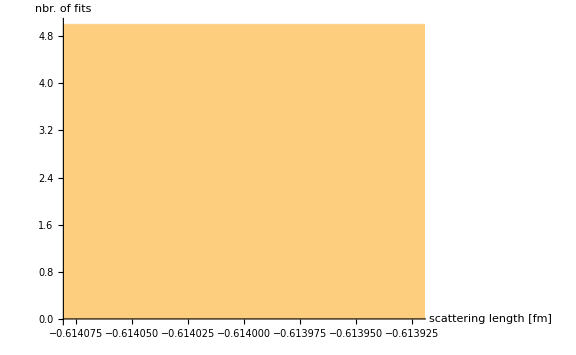

-Graphics3D-

```mathematica
cutoff=4.0;

JacobiWavefunctionPara=Select[JacobiWavefunctions,#[[1]]==cutoff&][[1]][[2]];
Rmax=4;
grdPoints=12;
r1r2Range=Subdivide[Rmax,grdPoints-1];
JacobiWavefunction=Total[#[[1]] Exp[-#[[2]] r1^2-#[[3]] r2^2]&/@JacobiWavefunctionPara];
JacobiWavefunction=JacobiWavefunction/Sqrt[norma];

JacobiWavefunctionSym=Total[#[[1]] (Exp[-#[[2]] r1^2-#[[3]] r2^2]+Exp[-#[[2]] r2^2-#[[3]] r1^2])&/@JacobiWavefunctionPara];
JacobiWavefunctionGrid=Table[JacobiWavefunction/.{r1->R1,r2->R2},{R1,r1r2Range},{R2,r1r2Range}];
JacobiWavefunctionSymGrid=Table[JacobiWavefunctionSym/.{r1->R1,r2->R2},{R1,r1r2Range},{R2,r1r2Range}];
JacobilWavefunctionGridFlat=Flatten[Table[{R1,R2,JacobiWavefunction/.{r1->R1,r2->R2}},{R1,r1r2Range},{R2,r1r2Range}],1];
fitfunctions={};
fits={};
scattlengths={};
fitDim=5;
rMax=8;
nGrd=80;
nIter=5;
Do[
Subscript[a, min]=RandomReal[{-100,-90}];
Subscript[a, max]=RandomReal[{90,100}];
Subscript[b, min]=RandomReal[{0,0}];
Subscript[b, max]=RandomReal[{10,31}];
{tmpCore,tmpFit}=FitCoreToGauss[fitDim,JacobilWavefunctionGridFlat,Subscript[a, min],Subscript[a, max],Subscript[b, min],Subscript[b, max]];
AppendTo[fitfunctions,tmpCore];
AppendTo[fits,tmpFit];
tmp=GetERE[cutoff,rMax,nGrd,tmpCore];

AppendTo[scattlengths,tmp[[1]]];

Print[nn,") a_(trimer - trimer) = ",scattlengths[[-1]],tmpCore]
,{nn,Range[nIter]}]
Histogram[scattlengths,{0.01},AxesLabel->{"scattering length [fm]","nbr. of fits"},PlotRange->{{Mean[scattlengths]-2 StandardDeviation[scattlengths],Mean[scattlengths]+2 StandardDeviation[scattlengths]},Automatic},ImageSize->Large]
selection=Range[nIter];
legends=Append[selection,"ψ_variational"];
fitsGrid=Table[Normal[#]/.{rrel1->R1,rrel2->R2},{R1,r1r2Range},{R2,r1r2Range}]&/@fits[[selection]];
ListPlot3D[Append[fitsGrid,JacobiWavefunctionGrid],PlotRange->Full,PlotLegends->legends,AxesLabel->{"|(ρ⃗)_1|  [fm]","|(ρ⃗)_2|  [fm]","∑a_n^(fit)·e^(-SubsuperscriptBox[b, n, (fit)] (SubsuperscriptBox[ρ, 1, 2] + SubsuperscriptBox[ρ, 2, 2]))"},ImageSize->Large]
```

symmetry of the wave function:
first, and foremost, I must not succumb to the fallacy of confusing rotational symmetry of a S-wave state, i.e., L_total=[[[[l_1⊗l_2]^l_12⊗l_3]^(l_((12)3))⊗l_4]^(l_(((12)3)4))⊗...]^L_total , with permutation symmetry.
In principle, the variational wave function is not guaranteed to be symmetric wrt. ρ_1↔ρ_2 interchange. The variational code obtains its optimal solution by anti-symmetrizing the total wave function,
which means that as long as the number of particles is less than the number of fermionic species, A<N_F, with N_F=4 for the two nuclear degrees of freedom, a totally anti-symmetric internal spin-isospin
wave function allows for a totally symmetric -- now wrt. any 𝔓(ermutation)∈𝔖_A(ymmetric group) -- spatial wave function.
The expansion coefficients in combination with a certain pair (for A=3) of width parameters (γ_i^(1,2)) does not reflect this symmetry explicitly if we choose different numerical values for γ_i^(1) and γ_i^(2)
ψ=𝔄^-[ Ξ⊗∑c_i·e^(-γ_i^(1)ρ_1^2)e^(-γ_i^(2)ρ_2^2) ]
Hence, we must adapt our cluster basis to 𝔄^+[∑c_i·e^(-γ_i^(1)ρ_1^2)e^(-γ_i^(2)ρ_2^2) ], i.e., the symmetrized spatial wave function.
ECCE:
i)  if a large set of widths was chosen, the symmetrization might already be realized (see examples below);
ii) (r̄)_1^2+(r̄)_2^2+(r̄)_3^2=(ρ⃗)_1^2+(ρ⃗)_2^2 (see coordinate_trafos.nb);

```mathematica
JacobiWavefunctionSymGrid//MatrixForm;
JacobiWavefunctionGrid//MatrixForm
```

(3.49126 | 2.79485 | 1.50778 | 0.686466 | 0.357365 | 0.197952 | 0.0867723 | 0.0110917 | -0.030335 | -0.043591 | -0.0378767 | -0.0225958 | -0.00533995 | 0.00897609 | 0.0180439 | 0.0215499 | 0.0203987 | 0.0160247 | 0.00990444 | 0.00327998 | -0.00294976 | -0.00823002 | -0.0122948 | -0.015092 | -0.0167102
2.86725 | 2.26193 | 1.17794 | 0.520009 | 0.27179 | 0.156781 | 0.0767072 | 0.0212486 | -0.0104066 | -0.0223508 | -0.0208664 | -0.0124125 | -0.00222677 | 0.00627975 | 0.0114815 | 0.0131228 | 0.0117866 | 0.00842248 | 0.00401221 | -0.000620038 | -0.00488265 | -0.00841731 | -0.0110612 | -0.0127955 | -0.0136956
1.46381 | 1.15113 | 0.608731 | 0.293356 | 0.175393 | 0.117167 | 0.0739821 | 0.0418295 | 0.0207225 | 0.00908042 | 0.00424191 | 0.00337883 | 0.00414039 | 0.00494438 | 0.00497778 | 0.00402645 | 0.0022494 | -0.000024579 | -0.00244208 | -0.00470813 | -0.00661968 | -0.00806696 | -0.00901802 | -0.00949729 | -0.00956461
0.548209 | 0.44847 | 0.27473 | 0.168475 | 0.119492 | 0.0876294 | 0.0613284 | 0.0404276 | 0.0252854 | 0.0152967 | 0.00924696 | 0.00577653 | 0.00371241 | 0.00222713 | 0.000852908 | -0.000591074 | -0.00210172 | -0.00358684 | -0.00493377 | -0.00604922 | -0.00687596 | -0.00739435 | -0.00761596 | -0.00757425 | -0.00731529
0.240725 | 0.21147 | 0.158189 | 0.11964 | 0.0940919 | 0.0725392 | 0.0533726 | 0.0374311 | 0.0251543 | 0.0163076 | 0.0102384 | 0.00615958 | 0.00335809 | 0.00130046 | -0.000347557 | -0.00175502 | -0.00298023 | -0.00402267 | -0.00486151 | -0.00547863 | -0.00586897 | -0.00604259 | -0.00602219 | -0.0058388 | -0.00552754
0.130915 | 0.123446 | 0.107735 | 0.0913579 | 0.0750691 | 0.0589092 | 0.0439646 | 0.0312189 | 0.0210964 | 0.0135164 | 0.00808241 | 0.00427699 | 0.00160785 | -0.000313504 | -0.00175131 | -0.00286203 | -0.00372619 | -0.00438012 | -0.00484031 | -0.00511842 | -0.00522875 | -0.00519044 | -0.00502687 | -0.00476386 | -0.00442765
0.0791732 | 0.0781821 | 0.0741436 | 0.0659027 | 0.0546675 | 0.0426293 | 0.0313333 | 0.0216302 | 0.0138685 | 0.00801779 | 0.00380974 | 0.000877903 | -0.00113593 | -0.00252272 | -0.00348863 | -0.00416419 | -0.00462491 | -0.00491262 | -0.00505213 | -0.00506176 | -0.00495889 | -0.00476189 | -0.00449022 | -0.00416356 | -0.00380084
0.0519513 | 0.0522431 | 0.0510058 | 0.0458632 | 0.037826 | 0.0289964 | 0.0206846 | 0.0135462 | 0.00784592 | 0.00356882 | 0.000523135 | -0.0015577 | -0.00293729 | -0.00383257 | -0.0044001 | -0.00474185 | -0.00491949 | -0.00496938 | -0.00491443 | -0.00477172 | -0.00455652 | -0.00428387 | -0.00396881 | -0.00362595 | -0.00326886
0.0357673 | 0.0360122 | 0.0351885 | 0.0315072 | 0.0256837 | 0.0192705 | 0.0132353 | 0.00806011 | 0.00394069 | 0.000868938 | -0.00129284 | -0.00273802 | -0.0036592 | -0.00421622 | -0.0045258 | -0.00466536 | -0.00468297 | -0.00460805 | -0.00445976 | -0.00425248 | -0.00399877 | -0.00371054 | -0.00339925 | -0.00307575 | -0.00274984
0.0245622 | 0.0245806 | 0.0237458 | 0.0210036 | 0.0168235 | 0.0122458 | 0.00794356 | 0.00426086 | 0.00133995 | -0.000822733 | -0.00232398 | -0.00330139 | -0.00389309 | -0.0042148 | -0.0043521 | -0.00436283 | -0.00428392 | -0.00413877 | -0.00394314 | -0.00370895 | -0.00344639 | -0.00316484 | -0.00287302 | -0.00257891 | -0.00228954
0.0160231 | 0.0158761 | 0.0150401 | 0.0130142 | 0.0100886 | 0.0069139 | 0.00393762 | 0.00139792 | -0.000604281 | -0.00206945 | -0.00306355 | -0.00368188 | -0.00402118 | -0.00416347 | -0.00417048 | -0.00408495 | -0.0039351 | -0.00373955 | -0.00351125 | -0.00326009 | -0.00299435 | -0.00272138 | -0.00244771 | -0.00217911 | -0.00192048
0.00941404 | 0.00918272 | 0.00840769 | 0.00694657 | 0.00496679 | 0.00284545 | 0.00086595 | -0.000812151 | -0.00211919 | -0.0030539 | -0.00365976 | -0.00400098 | -0.0041437 | -0.00414499 | -0.00404882 | -0.00388662 | -0.00368 | -0.00344389 | -0.00318899 | -0.00292358 | -0.00265438 | -0.0023871 | -0.0021266 | -0.0018769 | -0.00164123
0.00446587 | 0.00420986 | 0.00353639 | 0.00251035 | 0.00121997 | -0.000138446 | -0.00139493 | -0.00244616 | -0.00324534 | -0.00379043 | -0.00410925 | -0.00424403 | -0.00423918 | -0.00413396 | -0.00395957 | -0.00373923 | -0.00348968 | -0.00322302 | -0.00294825 | -0.00267229 | -0.00240067 | -0.00213783 | -0.0018873 | -0.00165182 | -0.00143338
0.000961458 | 0.000716445 | 0.000158185 | -0.000545404 | -0.00135396 | -0.0021832 | -0.00293776 | -0.00355282 | -0.00399766 | -0.00427009 | -0.00438751 | -0.00437726 | -0.00426893 | -0.00408954 | -0.00386141 | -0.00360197 | -0.00332444 | -0.00303883 | -0.00275276 | -0.00247212 | -0.00220146 | -0.00194429 | -0.00170318 | -0.0014799 | -0.00127556
-0.00135296 | -0.00156969 | -0.0020179 | -0.00249184 | -0.002978 | -0.00345654 | -0.00387855 | -0.00420448 | -0.00441445 | -0.00450649 | -0.00449134 | -0.00438668 | -0.00421236 | -0.00398724 | -0.00372767 | -0.00344707 | -0.00315613 | -0.00286327 | -0.00257506 | -0.00229654 | -0.00203155 | -0.00178286 | -0.00155235 | -0.00134116 | -0.00114977
-0.00274959 | -0.00293258 | -0.00328546 | -0.00360154 | -0.003881 | -0.00413756 | -0.00434959 | -0.00449341 | -0.00455625 | -0.00453645 | -0.00444072 | -0.00428067 | -0.00406996 | -0.00382216 | -0.00354963 | -0.00326303 | -0.00297125 | -0.00268148 | -0.00239942 | -0.00212948 | -0.00187488 | -0.00163789 | -0.00141991 | -0.00122163 | -0.00104316
-0.00348405 | -0.00363428 | -0.00390925 | -0.00411973 | -0.00427192 | -0.00439431 | -0.00448021 | -0.00451555 | -0.00449205 | -0.00440842 | -0.00426897 | -0.00408167 | -0.00385626 | -0.00360294 | -0.00333143 | -0.00305046 | -0.00276755 | -0.00248895 | -0.00221964 | -0.00196347 | -0.00172322 | -0.00150076 | -0.00129716 | -0.00111284 | -0.000947671
-0.00377132 | -0.00389249 | -0.00410568 | -0.00424658 | -0.0043232 | -0.00436822 | -0.00438236 | -0.00435717 | -0.00428715 | -0.00417137 | -0.00401279 | -0.00381715 | -0.00359181 | -0.00334477 | -0.00308392 | -0.00281662 | -0.00254933 | -0.00228751 | -0.00203554 | -0.0017968 | -0.0015737 | -0.0013678 | -0.00117996 | -0.00101041 | -0.000858912
-0.0037765 | -0.00387294 | -0.00403752 | -0.00413245 | -0.00416556 | -0.00416813 | -0.00414396 | -0.00408784 | -0.00399598 | -0.00386777 | -0.00370541 | -0.00351332 | -0.0032973 | -0.0030639 | -0.00281973 | -0.00257106 | -0.00232352 | -0.00208188 | -0.00185 | -0.00163084 | -0.0014265 | -0.00123832 | -0.00106697 | -0.000912597 | -0.000774903
-0.00361696 | -0.0036926 | -0.00381857 | -0.00388247 | -0.00389104 | -0.00387159 | -0.0038287 | -0.00375898 | -0.00365975 | -0.00353063 | -0.00337343 | -0.0031917 | -0.00299026 | -0.00277459 | -0.00255032 | -0.00232288 | -0.00209716 | -0.00187733 | -0.00166679 | -0.00146813 | -0.00128316 | -0.00111304 | -0.000958329 | -0.000819102 | -0.00069505
-0.0033705 | -0.00342863 | -0.00352335 | -0.00356544 | -0.00356029 | -0.00353024 | -0.00347955 | -0.00340585 | -0.00330721 | -0.00318346 | -0.00303615 | -0.00286829 | -0.00268395 | -0.00248782 | -0.00228475 | -0.00207943 | -0.00187612 | -0.00167846 | -0.0014894 | -0.00131121 | -0.00114547 | -0.000993152 | -0.000854739 | -0.000730264 | -0.000619426
-0.00308563 | -0.00312891 | -0.00319781 | -0.00322382 | -0.00321091 | -0.00317639 | -0.00312369 | -0.00305105 | -0.00295709 | -0.00284179 | -0.00270654 | -0.00255395 | -0.00238753 | -0.0022113 | -0.00202945 | -0.00184604 | -0.00166474 | -0.00148873 | -0.00132057 | -0.0011622 | -0.00101499 | -0.000879788 | -0.000756984 | -0.000646594 | -0.000548335
-0.00279084 | -0.00282146 | -0.00286873 | -0.00288231 | -0.00286491 | -0.0028291 | -0.00277732 | -0.00270822 | -0.0026208 | -0.0025152 | -0.00239269 | -0.00225555 | -0.00210682 | -0.00194997 | -0.00178859 | -0.00162619 | -0.00146593 | -0.00131052 | -0.00116218 | -0.00102257 | -0.000892877 | -0.000773812 | -0.000665701 | -0.000568546 | -0.000482088
-0.00250198 | -0.00252179 | -0.00255081 | -0.00255451 | -0.00253444 | -0.00249895 | -0.00244949 | -0.00238501 | -0.00230483 | -0.00220919 | -0.00209927 | -0.00197708 | -0.00184525 | -0.00170674 | -0.00156466 | -0.00142197 | -0.00128139 | -0.00114523 | -0.00101538 | -0.000893253 | -0.000779852 | -0.000675781 | -0.000581311 | -0.000496432 | -0.000420911
-0.00222735 | -0.00223801 | -0.00225167 | -0.00224738 | -0.00222573 | -0.00219137 | -0.00214486 | -0.00208538 | -0.00201251 | -0.00192657 | -0.00182867 | -0.00172057 | -0.00160454 | -0.0014831 | -0.00135889 | -0.00123443 | -0.00111201 | -0.000993593 | -0.000880755 | -0.000774702 | -0.000676273 | -0.000585973 | -0.000504023 | -0.000430406 | -0.000364913)

```mathematica
ii=2;
JacobiWavefunctionFit=Total[#[[1]] Exp[-#[[2]] (r1^2+ r2^2+(r1+r2)^2)]&/@fitfunctions[[ii]]]
1/Sqrt[NormTF[fitfunctions[[ii]]]]
norma=NIntegrate[(*r1^2 r2^2*) JacobiWavefunctionFit*JacobiWavefunctionFit,{r1,-120,120},{r2,-120,120}]
```

-1.23597 ⅇ^(-21.3265 (r1^2+r2^2+(r1+r2)^2))+90.7873 ⅇ^(-0.100475 (r1^2+r2^2+(r1+r2)^2))-90.1169 ⅇ^(-0.1 (r1^2+r2^2+(r1+r2)^2))

245.232

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

2.22299

```mathematica
NIntegrate[JacobiWavefunction*JacobiWavefunction,{r1,0,200},{r2,0,200}]
```

1.

```mathematica
ListPlot3D[{JacobiWavefunctionGrid},PlotLegends->{"ψ","𝔄^+ψ"},PlotRange->Full]
```

-Graphics3D-

open issues:
i)  sign of the wave function must not (?) affect observables, in general, the scattering lengths, in particular.
ii)

```mathematica
mat[N_]:=Table[If[row==col,2 "(2α)",1 "(2α)"],{row,1,N-1},{col,1,N-1}]
Do[
Print[nn,") ",mat[nn]//MatrixForm,"  |A|=",Det[mat[nn]]];
,{nn,1,10}];
```

Det::matsq: Argument {} at position 1 is not a non-empty square matrix.

1) {}  |A|=Det[{}]

2) (2 (2α))  |A|=2 (2α)

3) (2 (2α) | (2α)
(2α) | 2 (2α))  |A|=3 (2α)^2

4) (2 (2α) | (2α) | (2α)
(2α) | 2 (2α) | (2α)
(2α) | (2α) | 2 (2α))  |A|=4 (2α)^3

5) (2 (2α) | (2α) | (2α) | (2α)
(2α) | 2 (2α) | (2α) | (2α)
(2α) | (2α) | 2 (2α) | (2α)
(2α) | (2α) | (2α) | 2 (2α))  |A|=5 (2α)^4

6) (2 (2α) | (2α) | (2α) | (2α) | (2α)
(2α) | 2 (2α) | (2α) | (2α) | (2α)
(2α) | (2α) | 2 (2α) | (2α) | (2α)
(2α) | (2α) | (2α) | 2 (2α) | (2α)
(2α) | (2α) | (2α) | (2α) | 2 (2α))  |A|=6 (2α)^5

7) (2 (2α) | (2α) | (2α) | (2α) | (2α) | (2α)
(2α) | 2 (2α) | (2α) | (2α) | (2α) | (2α)
(2α) | (2α) | 2 (2α) | (2α) | (2α) | (2α)
(2α) | (2α) | (2α) | 2 (2α) | (2α) | (2α)
(2α) | (2α) | (2α) | (2α) | 2 (2α) | (2α)
(2α) | (2α) | (2α) | (2α) | (2α) | 2 (2α))  |A|=7 (2α)^6

8) (2 (2α) | (2α) | (2α) | (2α) | (2α) | (2α) | (2α)
(2α) | 2 (2α) | (2α) | (2α) | (2α) | (2α) | (2α)
(2α) | (2α) | 2 (2α) | (2α) | (2α) | (2α) | (2α)
(2α) | (2α) | (2α) | 2 (2α) | (2α) | (2α) | (2α)
(2α) | (2α) | (2α) | (2α) | 2 (2α) | (2α) | (2α)
(2α) | (2α) | (2α) | (2α) | (2α) | 2 (2α) | (2α)
(2α) | (2α) | (2α) | (2α) | (2α) | (2α) | 2 (2α))  |A|=8 (2α)^7

9) (2 (2α) | (2α) | (2α) | (2α) | (2α) | (2α) | (2α) | (2α)
(2α) | 2 (2α) | (2α) | (2α) | (2α) | (2α) | (2α) | (2α)
(2α) | (2α) | 2 (2α) | (2α) | (2α) | (2α) | (2α) | (2α)
(2α) | (2α) | (2α) | 2 (2α) | (2α) | (2α) | (2α) | (2α)
(2α) | (2α) | (2α) | (2α) | 2 (2α) | (2α) | (2α) | (2α)
(2α) | (2α) | (2α) | (2α) | (2α) | 2 (2α) | (2α) | (2α)
(2α) | (2α) | (2α) | (2α) | (2α) | (2α) | 2 (2α) | (2α)
(2α) | (2α) | (2α) | (2α) | (2α) | (2α) | (2α) | 2 (2α))  |A|=9 (2α)^8

10) (2 (2α) | (2α) | (2α) | (2α) | (2α) | (2α) | (2α) | (2α) | (2α)
(2α) | 2 (2α) | (2α) | (2α) | (2α) | (2α) | (2α) | (2α) | (2α)
(2α) | (2α) | 2 (2α) | (2α) | (2α) | (2α) | (2α) | (2α) | (2α)
(2α) | (2α) | (2α) | 2 (2α) | (2α) | (2α) | (2α) | (2α) | (2α)
(2α) | (2α) | (2α) | (2α) | 2 (2α) | (2α) | (2α) | (2α) | (2α)
(2α) | (2α) | (2α) | (2α) | (2α) | 2 (2α) | (2α) | (2α) | (2α)
(2α) | (2α) | (2α) | (2α) | (2α) | (2α) | 2 (2α) | (2α) | (2α)
(2α) | (2α) | (2α) | (2α) | (2α) | (2α) | (2α) | 2 (2α) | (2α)
(2α) | (2α) | (2α) | (2α) | (2α) | (2α) | (2α) | (2α) | 2 (2α))  |A|=10 (2α)^9

```mathematica
NormTF[testcore]/(1/√(NormT[testcore]^2))
```

84.4714

```mathematica
bnd=20;
testcore={{13.3,1.5},{103.3,2.5}};
unfi=testcore;
NormT[core_,N_:3]:=Total[Table[core[[ii]][[1]] core[[jj]][[1]] (Pi^(N-1)/(N (core[[ii]][[2]]+core[[jj]][[2]])^(N-1)))^(3/2),{ii,1,Length[core]},{jj,1,Length[core]}],2]
no=NormT[unfi];
(*Print["---------------------"]
Print["Norm=",no]
Print["---------------------"]
nfifu={#[[1]]/√no,#[[2]]}&/@unfi;
Print["Normalized: "];
nofi=1/(√no) Total[#[[1]] Exp[-#[[2]] (2 r1^2+2 r2^2+2 (r1 r2))]&/@unfi]
numi1=NIntegrate[(2 Pi)^2 r1^2 r2^2 nofi*nofi,{r1,0,bnd},{r2,0,bnd}]
*)
Print["---------------------"]
Print["Unnormalized: "];
unofi=Total[#[[1]] Exp[-#[[2]] (2 (rx1^2+ry1^2+rz1^2)+2 (rx2^2+ry2^2+rz2^2)+2 (rx1 rx2+ry1 ry2+rz1 rz2))]&/@unfi]
numi2=NIntegrate[unofi*unofi,{rx1,-bnd,bnd},{rx2,-bnd,bnd},{ry1,-bnd,bnd},{ry2,-bnd,bnd},{rz1,-bnd,bnd},{rz2,-bnd,bnd}];
Print["∫_0^(2  π) dϕ∫_-1^1 d(cosθ)∫ρ^2dρ Ψ^*Ψ = ",numi2,"=^?",no]
NormTF[testcore]/(1/√(NormT[testcore]^2))
Print["---------------------"]
```

---------------------

Unnormalized:

103.3 ⅇ^(-2.5 (2 (rx1^2+ry1^2+rz1^2)+2 (rx1 rx2+ry1 ry2+rz1 rz2)+2 (rx2^2+ry2^2+rz2^2)))+13.3 ⅇ^(-1.5 (2 (rx1^2+ry1^2+rz1^2)+2 (rx1 rx2+ry1 ry2+rz1 rz2)+2 (rx2^2+ry2^2+rz2^2)))

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 805.023 and 2.82979 for the integral and error estimates.

∫_0^(2  π) dϕ∫_-1^1 d(cosθ)∫ρ^2dρ Ψ^*Ψ = 805.023=^?804.688

84.4714

---------------------